# Impact of Q2-dependence of alphas_s in Sudakov definition

## Parametrization of the strong-coupling constant

## We try first to introduce a Q2-dependent expression for alphas_s. We do that by fitting a standard plot for the alphas_s as a function of Q2 (https://pdg.lbl.gov/2019/reviews/rpp2019-rev-qcd.pdf). Be aware that the PDG plot is f(Q) while our parametrization is a function of Q2

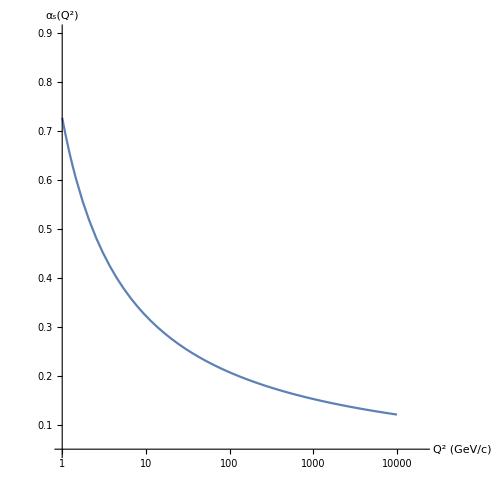

0.120741

```mathematica
LambdaQCD=0.4;
Bethazero = 0.75;
alphas[Q2_]:=1/(Bethazero*Log[Q2/(LambdaQCD*LambdaQCD)]) ;
LogLinearPlot[alphas[Q2],{Q2,1,10000}, Axes->True,AxesLabel->{"Q^2 (GeV/c)","α_s(Q^2)"},PlotRange->{{1,20000},{0.05,0.9}},AspectRatio->1,LabelStyle->{FontSize->22,FontFamily->"Arial", ,Black}, ImageSize->500]
alphas[10000]
```

## Sudakov with α_s=0.12 and α_s(Q^2)

{x→11.3018}

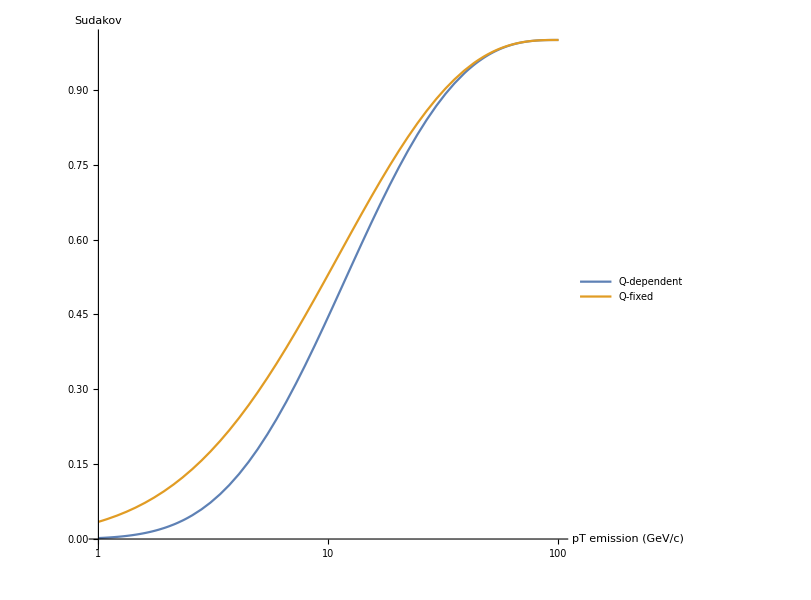

```mathematica
Clear[sudakovQfixed,sudakovQ];
pt1=100.;
sudakovQ[pt0_?NumericQ]:=Exp[-1/Pi*NIntegrate[1/(2Q2)* alphas[Q2]*Pgtoggvacuum[z,Q2],{z, pt0/pt1,1},{Q2, pt0*pt0/z,z*pt1*pt1}]]//.{pt1->100}
sudakovQfixed[pt0_?NumericQ]:=Exp[-1/Pi*NIntegrate[1/(2Q2)* alphas[10000]*Pgtoggvacuum[z,Q2],{z, pt0/pt1,1},{Q2, pt0*pt0/z,z*pt1*pt1}]]//.{pt1->100}
FindRoot[sudakovQ[x]==0.5,{x,1,100}]
LogLinearPlot[{sudakovQ[x],sudakovQfixed[x]},{x,1,100} , PlotLegends->{"Q-dependent", "Q-fixed"},AxesLabel->{"     pT emission (GeV/c)","Sudakov"},PlotRange->{{1,100},{0.0,1.0}},AspectRatio->1,LabelStyle->{FontSize->22,FontFamily->"Arial", ,Black}, ImageSize->600]
```